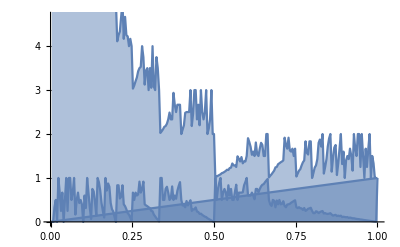

-Graphics3D-

```mathematica
n=250;
X=Range[n]/n;
f[q_]:=Module[{a=ContinuedFraction[q],a1=List[],a2=List[],i},
For[i=1,i<=Length[a],i=i+2,
AppendTo[a1,a[[i]]]
];
For[i=2,i<=Length[a],i=i+2,
AppendTo[a2,a[[i]]]
];
Return[{1/ContinuedFractionK[Indexed[a1,i],{i,1,Length[a1]}],
1/ContinuedFractionK[Indexed[a2,i],{i,1,Length[a2]}]}]
]
DiscretePlot[Prepend[f[q],q],{q,0,1,1/n}]
g[q_,r_]:=Module[{a1=ContinuedFraction[q],a2=ContinuedFraction[r],a=List[],max,i},
max=Min[Length[a1],Length[a2]];
For[i=1,Length[a1]<=max,i++,
AppendTo[a1,0]
];
For[i=1,Length[a2]<=max,i++,
AppendTo[a2,0]
];
For[i=1,i<=max,i++,
AppendTo[AppendTo[a,a1[[i]]],a2[[i]]]
];
Return[1/ContinuedFractionK[Indexed[a,i],{i,1,Length[a]}]]
]
DiscretePlot3D[g[q,r],{q,0,1,1/n},{r,0,1,1/n}]
```